```mathematica
xml=Import[NotebookDirectory[]<>"~images\\"<>"engine_naive.xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname,plotpath,imagepath}=xml;
tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
alpha=(#/255.&)/@a;
index=Flatten@Position[alpha,_?(#>0&)];
chartcolors=rgbcolors[[#]]&/@index;
```

```mathematica
img={-Graphics-,-Graphics-};mixed=-Graphics-;
```

```mathematica
dist=ParallelMap[ColorDistance[#,mixed]&,img];
sum=ImageAdd[dist[[1]],dist[[2]]];
weight=ParallelMap[ImageApply[If[#2≠0,#1/#2,0]&,{#,sum}]&,Reverse@dist];
saliency=ImageSaliencyFilter[mixed]
overlap=ParallelMap[ImageMultiply[saliency,#]&,weight]
ImageMeasurements[saliency,"TotalIntensity"]
features=ImageMeasurements[#,"TotalIntensity"]&/@overlap
Total[features]
features/Total[features]
```

9156.69

{3196.12,2527.51}

5723.63

{0.558408,0.441592}

```mathematica
size=First@ImageDimensions[mixed]/16;
left=ImageSubtract[saliency,overlap[[1]]]//ImageSubtract[#,overlap[[2]]]&
gaussian=ParallelMap[GaussianFilter[#,size]&,overlap];
ImageAdjust/@gaussian
sumOfGaussian=ImageAdd[gaussian[[1]],gaussian[[2]]];
ratio=ParallelMap[ImageApply[If[#2≠0,Clip[#1/#2],0]&,{#,sumOfGaussian}]&,gaussian];
leftGaussian=ParallelMap[ImageMultiply[left,#]&,ratio]
weightedSaliency=Table[ImageAdd[overlap[[i]],leftGaussian[[i]]],{i,Length[leftGaussian]}]
ImageMeasurements[saliency,"TotalIntensity"]
features2=ImageMeasurements[#,"TotalIntensity"]&/@weightedSaliency
Total[features2]
metric=features2/Total[features2]
```

9156.69

{5003.84,3861.94}

8865.77

{0.564399,0.435601}

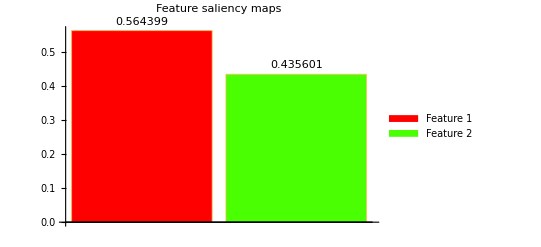

```mathematica
legends={"Feature 1","Feature 2","Feature 3","Feature 4"};
BarChart[metric,PlotLabel->"Feature saliency maps",ChartLegends->legends,ChartLabels->Placed[ToString/@metric,Above],ChartStyle->chartcolors]
```